## To solve the puzzle: the size of a Truncated Gaussian Beam at the foci.

Adopted the equation given by Vinay Ramasesh’s thesis, Eq. (4.6) (4.7). They are also simple Fourier optics equations in textbooks. 
g[x0,y0] is the truncated gaussian electric field after the lens aperture. The lens we used here is Thorlabs AL50100H.

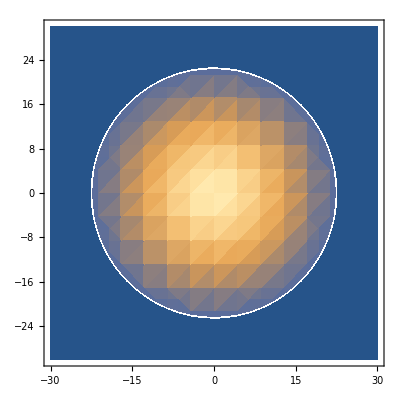

-Graphics3D-

```mathematica
g[x0_,y0_]:=E^(-(x0^2+y0^2)/w^2)*(UnitStep[Dia/2-Sqrt[x0^2+y0^2]])
w=16;
Dia=45;
λ=741*10^(-6);
f2=100;  (*Units are all in millimeters*)

DensityPlot[g[x,y],{x,-30,30},{y,-30,30}]
TableA=Table[g[x,y],{x,-30,30,1},{y,-30,30,1}];
ListPlot3D[TableA]
u[x_,y_]:=NIntegrate[g[x0,y0]*E^(I*2*Pi/λ/f2*(x*x0+y*y0)),{x0,-25,25},{y0,-25,25}]
```

Note that we give an upper limit for the numerical integrate. If the pin hole is larger than this upper limit, then the integrate might lose some intensity out of the ROI.

```mathematica
IntenuI=Table[Abs[u[x,y]]^2,{x,0,2*10^-3,10^-4},{y,0,2*10^-3,10^-4}]
```

{480155.,477148.,468229.,453695.,434026.,409859.,381958.,351179.,318428.,284621.,250644.,217321.,185378.,155427.,127942.,103261.,81578.6,62956.9,47339.8,34570.7,24413.9,16577.7,10737.6,6557.43,3708.26,1883.52}

FittedModel[484748. ⅇ^(-0.00681328 (-1+x)^2)]

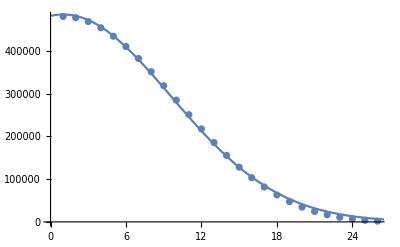

1.71331×10^-6

```mathematica
step=1*10^-4;
IntenuI2=Table[Abs[u[x,y]]^2,{x,0,2.5*10^-3,step},{y,0,0,10^-4}];
IntenuI2=Flatten[IntenuI2]
nlm=NonlinearModelFit[IntenuI2,A*E^(-2*(x-1)^2/ω^2),{A,ω},x]
Show[ListPlot[IntenuI2],Plot[nlm[x],{x,0,42}]]
myω=Abs[ω /.  nlm["BestFitParameters"]]*step*10^-3 (*Shows the fitted beam waist in the unit of meters*)
```

Conclusion: 
When the beam is infinitely large, the fitted waist of a airy disk is roughly 1.25 um.This value agrees with the equation given by Wikipedia-Airy disk-Approximation using a Gaussian profile.
When the beam is small enough or the aperture is big enough, the fitted waist is an ideal Gaussian, waist perfectly agrees with the Gaussian optics, about 1.47 um.
When we use a truncated Gaussian beam, waist w= 16 mm, clear aperture Dia =45 mm, the fitted beam waist is 1.72 um. Very close to our measurement.
1.72 is slightly smaller than Sqrt[1.25^2+1.47^2], because we are convolving a Bessel function and a Gaussian, instead of two Gaussians.